#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
(*Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]*)
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];
parity="-";
jJ=0.5;
mJs=Range[-jJ,jJ,1];
mom =0.001/198;
threshold=10^(-13);
```

```mathematica
ClearAll;
ImgSize=900;
SetDirectory["/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan_M/results"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan_M/results

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Eigensystem[norm],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];n=Length[Select[es[[1]],#<cutoff&]];ovsq=DiagonalMatrix[SparseArray[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]]];ovsqi=DiagonalMatrix[SparseArray[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

### Read LHS ⟨ ϕ_(3He)^n|(Ĥ)_(V18+UIX)|ϕ_(3He)^m ⟩, m,n∈{1,N_He3}

```mathematica
HeNormHamMat=readREAL8list["./mat_npp0.5^+"];
HeBasisDim=IntegerPart[Sqrt[Length[HeNormHamMat] 0.5]];
HeNorm=ArrayReshape[HeNormHamMat[[1;;HeBasisDim^2]],{HeBasisDim,HeBasisDim}];HeHam=ArrayReshape[HeNormHamMat[[HeBasisDim^2+1;;]],{HeBasisDim,HeBasisDim}];
```

```mathematica
{HeNmh,HeNmhi}=matSqrts[HeNorm,0];
```

min/max: {-1.95196×10^-14,369.91}

(min/max) discarded elements: 60 {-1.95196×10^-14,-1.10162×10^-18}

```mathematica
tst=Transpose[HeNmhi].HeNorm.HeNmhi;
```

#### Check zero mode norm eigenvectors are approximately zero mode eigenvectors of H

```mathematica
tv=Transpose[Eigensystem[HeNorm]][[-2]];
```

```mathematica
tv[[1]]
```

-2.89661×10^-18

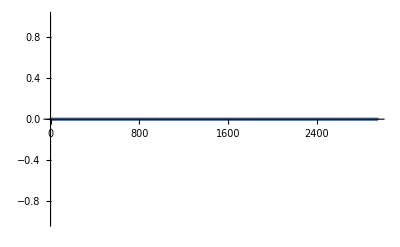

```mathematica
ListPlot[Chop[HeHam.tv[[2]],10^-6],PlotRange->Full]
```

```mathematica
tv=Transpose[Eigensystem[HeNorm]][[-4]];
```

```mathematica
tv[[1]]
```

5.3915×10^-18

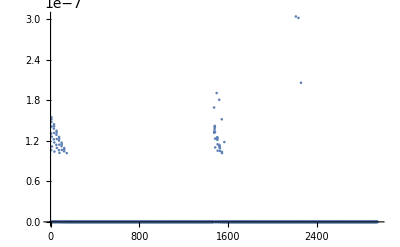

```mathematica
ListPlot[Chop[HeHam.tv[[2]],10^-7],PlotRange->Full]
```

#### The real calculation

Set a sensible cut-off

```mathematica
{HeNmh,HeNmhi}=matSqrts[HeNorm,threshold];
```

min/max: {-1.95196×10^-14,369.91}

(min/max) discarded elements: 1232 {-1.95196×10^-14,9.96747×10^-14}

```mathematica
{e0,v0}=Sort[Transpose[Eigensystem[tst=Transpose[HeNmhi].HeHam.HeNmhi;tst=(tst+Transpose[tst])/2]],#1[[1]]<#2[[1]]&][[1]];
e0
```

-7.21459

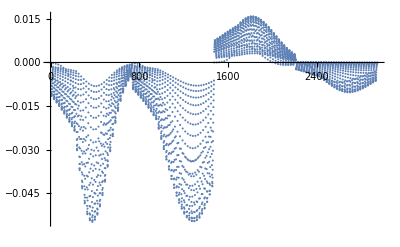

```mathematica
fullv0=Normalize[Transpose[HeNmh].v0];
ListPlot[fullv0]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
LitNormHamMat=readREAL8list["./mat_"<>ToString[jJ]<>"^"<>parity];
LITbasisDim=IntegerPart[Sqrt[Length[LitNormHamMat] 0.5]];
LitNorm=ArrayReshape[LitNormHamMat[[1;;LITbasisDim^2]],{LITbasisDim,LITbasisDim}];LitHam=ArrayReshape[LitNormHamMat[[LITbasisDim^2+1;;]],{LITbasisDim,LITbasisDim}];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = 2944

```mathematica
{LitNmh,LitNmhi}=matSqrts[LitNorm,0];
```

min/max: {-2.09689×10^-14,203.08}

(min/max) discarded elements: 140 {-2.09689×10^-14,-9.27777×10^-20}

#### Check zero mode norm eigenvectors are approximately zero mode eigenvectors of H

```mathematica
tv=Transpose[Eigensystem[LitNorm]][[-2]];
```

```mathematica
tv[[1]]
```

-9.27777×10^-20

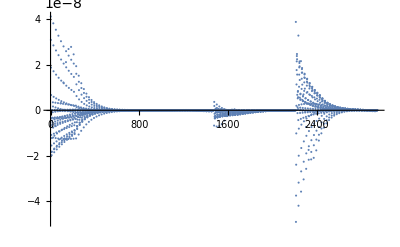

```mathematica
ListPlot[Chop[LitHam.tv[[2]],10^-16],PlotRange->Full]
```

```mathematica
tv=Transpose[Eigensystem[LitNorm]][[-4]];
```

```mathematica
tv[[1]]
```

-2.38732×10^-18

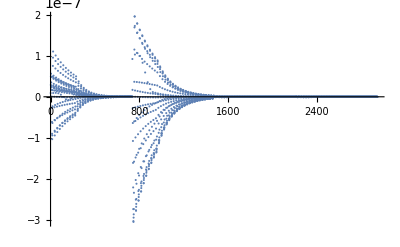

```mathematica
ListPlot[Chop[LitHam.tv[[2]],10^-17],PlotRange->Full]
```

#### Read RHS ⟨ ϕ_(lit+He3)^n|O_Lm_L|ϕ_(lit+He3)^m ⟩, n,m∈{1,N_LIT/n_k+N_He3}

the calculation is parallel in n_k parts

```mathematica
nk=Max[ToExpression[StringSplit[FileNames["*_inhomo*"],"_"][[All,1]]]];
ks=Range[0,nk];
mJ=mJs[[1]];
mL=mLs[[1]];
If[Abs[mJ-mL]≤1/2,
files="./"<>ToString[#]<>"_inhomo1-1_J"<>ToString[jJ]<>"_mJ"<>ToString[mJ]<>"-mL"<>ToString[mL]<>".log"&/@ks,
files="./"<>ToString[#]<>"_inhomo1-1_J"<>ToString[jJ]<>"_mJ"<>ToString[mJ]<>"-mL"<>ToString[-mL]<>".log"&/@ks
]

inhomos=SparseArray[readREAL8list[#]]&/@files;
CouplingMatrices=SparseArray[ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]]&/@inhomos;
```

{./0_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./1_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./2_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./3_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./4_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./5_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./6_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./7_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./8_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./9_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./10_inhomo1-1_J0.5_mJ-0.5-mL-1.log,./11_inhomo1-1_J0.5_mJ-0.5-mL-1.log}

#### Read expansion coefficients of He3 |He3 ⟩=∑_(m=1)^N_He3 c_m·|ϕ_He3^m ⟩

```mathematica
(*coeffs=RandomReal[{0,10^(-1)},HeBasisDim];*)
coeffs=fullv0;
Print["N_He3 = ",Length[coeffs]," = ",HeBasisDim,"  ⟨0|0⟩ = ",Norm[coeffs]];
```

N_He3 = 2944 = 2944  ⟨0|0⟩ = 1.

#### calculate the components of the RHS inhomogeneity vector by summing up the ME’s of one row with each column weighted by the corresponding |He3 ⟩ coefficient

```mathematica
CouplingBloxx=#[[HeBasisDim+1;;,;;HeBasisDim]]&/@CouplingMatrices;
RHSComponents=#.coeffs&/@CouplingBloxx;
RHSVector=Flatten[RHSComponents];
If[Length[RHSVector]≠LITbasisDim,Print["LIT state dimension of RHS("<>ToString[Length[RHSVector]]<>") and LHS("<>ToString[LITbasisDim]<>") inconsistent!"]]
Dimensions[CouplingBloxx[[#]]]&/@Range[Length[CouplingBloxx]]
```

{{253,2944},{253,2944},{230,2944},{253,2944},{253,2944},{230,2944},{253,2944},{253,2944},{230,2944},{253,2944},{253,2944},{230,2944}}

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=5.;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
testfu=0;
inhomo=(2/mom) RHSVector;
```

```mathematica
Clear[normreg];
normreg[threshold_]:=Block[
{es=Eigensystem[LitNorm],μ,transf,μs,Or},
{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];
If[Dimensions[μ]<Dimensions[es[[1]]],
{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];
,{μs,Or}={{},{}}];
{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}];

Clear[decompose];
decompose[threshold_]:= Block[{Oμ,Or,μs,oλs,otrf},
{Oμ,Or,μs}=normreg[threshold];{λs,trf}=Eigensystem[(Transpose[Oμ].LitHam).Oμ];{λs,trf.(Transpose[Oμ].inhomo)}
];
Clear[litcomp];
litcomp[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},Plus@@((Abs[#[[2]]]^2/((#[[1]]-e0-σRe)^2+σI^2))&/@λscf)];
```

```mathematica
testcompo={};testfu=0;
testfu+=Evaluate[litcomp[threshold]];
tmps=Transpose[decompose[threshold]];
testcompo=AppendTo[testcompo,Re[tmps]];

LIT=(-1)^(jJ-0.5) testfu;
LITcompo=Flatten[testcompo,1];

LITcompo=Transpose[{LITcompo[[All,1]],Re[(-1)^(jJ-0.5) LITcompo[[All,2]]]}];
```

```mathematica
Plot[LIT,{σRe,-10,120},PlotRange->{Automatic,Full},MaxRecursion->0,PlotPoints->500,MeshFunctions->{#&},Mesh->60,MeshStyle->PointSize[Large],
PlotLabel->"EV basis N_ev > "<>ToString[N[threshold],TraditionalForm]<>"   σ_I = "<>ToString[σI],AxesLabel->{Style["σ_R [MeV]",Blue,18],Style["LIT [fm^3 × MeV^-1]",Blue,18]},ImageSize->ImgSize,PlotLegends->{"J="<>ToString[jJ]},ImageSize->ImgSize]
```

-Graphics-

```mathematica
strengthfunctionBare=Transpose[{LITcompo[[All,1]],(LITcompo[[All,2]]^2)}];
ListPlot[strengthfunctionBare,Joined->False,PlotMarkers->Automatic,Filling->Axis,FillingStyle->Green,PlotRange->{{-10,120},Full},AxesLabel->{Style["E [MeV]",Blue,18],Style["SubsuperscriptBox[F, ν' L', νL, SubscriptBox[I, n], SubscriptBox[I, i] = SubscriptBox[I, f] = 1/2](k,k) [fm^3]",Blue,18]},PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[ks]]]]&[Floor[i-1,1]+1],{i,1,Length[ks]}],PlotLegends->{"I_n="<>ToString[jJ]},ImageSize->ImgSize]
```

-Graphics-

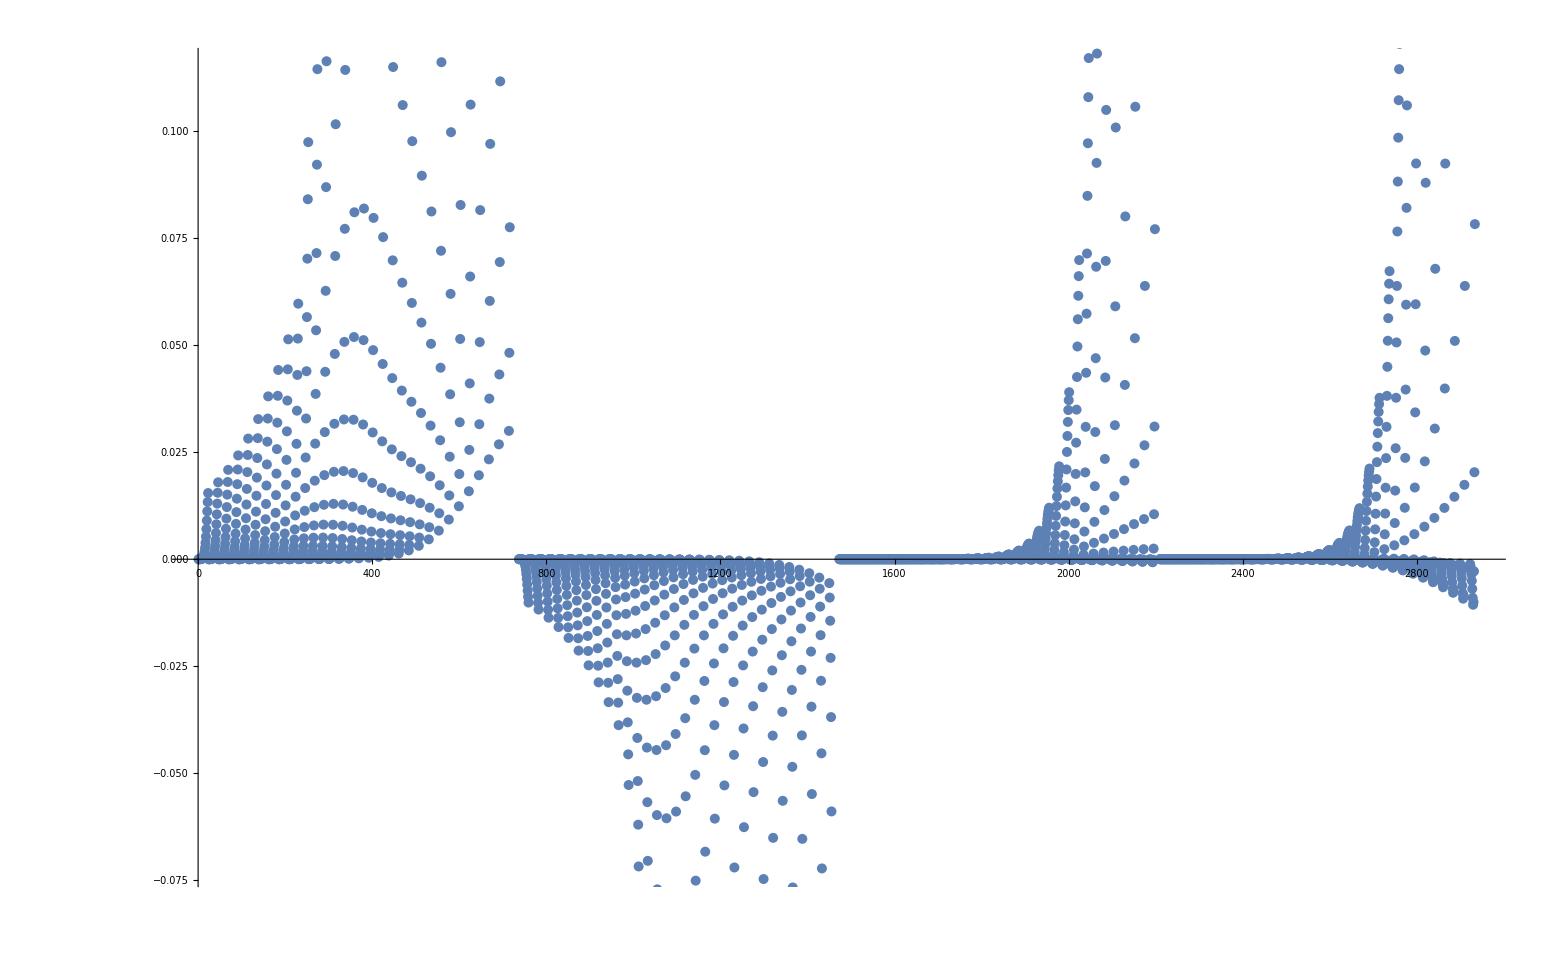

```mathematica
ListPlot[RHSVector]
```